```mathematica
ClearAll["Global`*"] ;(*clear any symbols you create*)
```

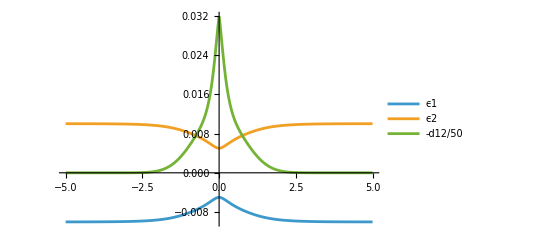

C:\Git\scripts\other\Python\fssh_simple_avoided_crossing\data\potentila.pdf

```mathematica
(* define electronic Hamiltonian *)
A0 = 0.01;
B0=1.6;
C0 = 0.005;
D0 = 1.0;
Vplus = ({{A0(1-ⅇ^(-B0 x)), C0 ⅇ^(-D0 x^2)}, {C0 ⅇ^(-D0 x^2), -A0(1-ⅇ^(-B0 x))}});
Vminus = ({{-A0(1-ⅇ^(B0 x)), C0 ⅇ^(-D0 x^2)}, {C0 ⅇ^(-D0 x^2), A0(1-ⅇ^(B0 x))}});

(* solve electronic Hamiltonian *)
{ϵ1p,ϵ2p} = Eigenvalues[Vplus];
{ϵ1m,ϵ2m} = Eigenvalues[Vminus];
{v1p,v2p} = Eigenvectors[Vplus];
v1p/=Sqrt[v1p.v1p];v2p/=Sqrt[v2p.v2p];
{v1m,v2m} = Eigenvectors[Vminus];
v1m/=Sqrt[v1m.v1m];v2m/=Sqrt[v2m.v2m];

(* find nonadiabatic coupling of adiabatic states *)
d12p = v1p.D[v2p, x];
d12m = v1m.D[v2m, x];

ϵ1[x_]:=If[x>0,ϵ1p,ϵ1m];
ϵ2[x_]:=If[x>0,ϵ2p,ϵ2m];
d12[x_]:=If[Abs[x]>5,0,If[x>0,d12p,d12m] ];

(* check surfaces *)
pic=Plot[{ϵ1[x], ϵ2[x], -d12[x]/50.}, {x, -5, 5}, 
 PlotLegends -> {"ϵ1", "ϵ2", "-d12/50"}]
Export[NotebookDirectory[]<>"potentila.pdf",pic,ImageSize->2400]
```

```mathematica
linspace[start_,end_,n_:100]:=Table[N[x],{x,start,end,(end-start)/(n-1)}];
xgrid = linspace[-10,10,100];
Export[NotebookDirectory[]<>"Tully-model1-e1.dat",Table[{x,ϵ1[x]},{x,xgrid}]]
Export[NotebookDirectory[]<>"Tully-model1-e2.dat",Table[{x,ϵ2[x]},{x,xgrid}]]
Export[NotebookDirectory[]<>"Tully-model1-d12.dat",Table[{x,d12[x]},{x,xgrid}]]
```

C:\Git\scripts\other\Python\fssh_simple_avoided_crossing\data\Tully-model1-e1.dat

C:\Git\scripts\other\Python\fssh_simple_avoided_crossing\data\Tully-model1-e2.dat

C:\Git\scripts\other\Python\fssh_simple_avoided_crossing\data\Tully-model1-d12.dat